```mathematica
ResourceFunction["DarkMode"][]
SetOptions[EvaluationNotebook[],Background->RGBColor[14/255,14/255,14/255]]
```

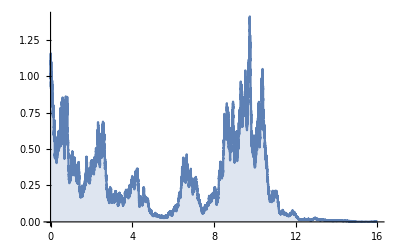

```mathematica
sample=RandomFunction[GeometricBrownianMotionProcess[0,1,1],{0,16,0.001}];
ListLinePlot[sample,Filling->Axis,PlotRange->Full,BaseStyle->{FontWeight->"Bold",FontSize->16}]
```